# Introduction to Quantum Optimization

This course provides a practical introduction to Quantum Optimization through the Wolfram Quantum Framework combined with modern quantum libraries.  It explores the foundations of Variational Quantum Algorithms (VQAs), including parametrized circuits, cost functions, and optimization strategies, and advances to key methods such as the Variational Quantum Eigensolver (VQE) and the Quantum Approximate Optimization Algorithm (QAOA) for tackling problems in quantum chemistry and combinatorial optimization. Students also learn advanced techniques like Quantum Natural Gradient Descent (QNGD) and Quantum Linear Solvers (QLS), from the HHL algorithm to variational and multiplexer-based approaches.

By Sebastián Rodríguez

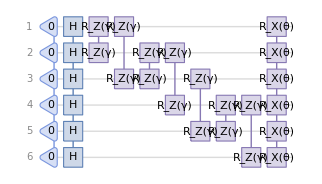
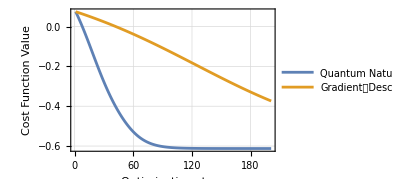
```mathematica
-Graphics--Graphics--Graphics-
```

Wolfram U Course (videos): https://www.wolfram.com/wolfram-u/courses/mathematics/wsg63-quantum-optimization/

## Summary

Quantum computing has the potential to address complex optimization problems that classical computers find challenging. Optimization is one of the most promising areas. It is integral to various fields, including logistics, finance, and AI. Any improvements from quantum algorithms could enhance solution quality, diversity, speed, and cost efficiency.

In the present Quantum Optimization course, we explore Variational Quantum Algorithms (VQAs), a leading framework to tackle optimization problems using today’s early-stage quantum devices. VQAs take a hybrid quantum-classical approach, using parameterized quantum circuits that learn optimal solutions through classical optimization.

#### Relevant Wolfram Mathematica functionalities

```mathematica
Dataset[{<|"Section"->"Wolfram Mathematica","Groups"->{<|"Category"->"Minimization","Items"->{"NMinimize","NMaximize","MinValue"}|>,<|"Category"->"Visualization","Items"->{"ContourPlot","StreamPlot"}|>,<|"Category"->"Graphs and Networks","Items"->{"Graph","VertexList","EdgeList"}|>}|>,<|"Section"->Hyperlink["  Wolfram Quantum Framework","https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/"],"Groups"->{<|"Category"->"QuantumOperator & QuantumCircuitOperator","Items"->{"Diagram","Table","Parameters","Matrix"}|>,<|"Category"->"QuantumState","Items"->{"Formula","StateVector","ProbabilityPlot"}|>,<|"Category"->"Measurements","Items"->{"QuantumDistance"}|>}|>,<|"Section"->Hyperlink["  Quantum Optimization Paclet","https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/tutorial/QuantumOptimization.html"],"Groups"->{<|"Category"->"Parametrized Circuits","Items"->{"GenerateParameters","ParametrizedLayer","EntanglementLayer"}|>,<|"Category"->"Gradient Methods","Items"->{"GradientDescent","QuantumNaturalGradientDescent","FubiniStudyMetricTensor"}|>,<|"Category"->"Mathematics","Items"->{"QuantumLinearSolve"}|>}|>}]
```

### Variational Quantum Eigensolver

Quantum chemistry meets quantum computing through the Variational Quantum Eigensolver (VQE), a powerful algorithm designed to find a molecule’s minimal energy state by approximating its ground state energy. Since molecular energy depends on the positions of atomic nuclei, this becomes a complex optimization problem where quantum algorithms excel. Using parameterized quantum circuits, VQE identifies the most stable molecular configurations, playing a crucial role in applications like drug discovery and materials science.

In the Wolfram Quantum Framework, we can symbolically calculate the variational states to obtain explicit expressions for the expectation value of the Hamiltonian we aim to minimize. By using symbolic QuantumCircuitOperator functions for parameterized circuits, we can construct these variational states and seamlessly perform the optimization using powerful minimization methods in Wolfram Mathematica, such as NMinimize. This symbolic approach provides deeper analytical insights and enhances the efficiency of optimization techniques like VQE.

### Quantum Approximate Optimization Algorithm

Optimization is at the core of many real-world challenges, and combinatorial problems are among the hardest to solve efficiently. One such problem is Max-Cut, where the goal is to split a graph into two sets while maximizing the number of edges between them—a fundamental task in network design, clustering, and AI.

Enter QAOA: a hybrid quantum-classical algorithm that leverages parameterized quantum circuits to tackle combinatorial optimization problems like Max-Cut. But how do we design the best ansatz for the task?

Using symbolic features in the Wolfram Quantum Framework and native Graph functionalities in Wolfram Mathematica, we gain deeper insights into ansatz design, enabling a more structured and analytical approach. By symbolically representing QAOA circuits, we are able to:

Optimize ansatz structures for better performance.

Visualize quantum operations at a higher level.

Explore parameter landscapes before execution.

This symbolic approach allows us to push QAOA further, enhancing its effectiveness for real-world applications.

### Quantum Natural Gradient Descent

In quantum computing, optimizing parameterized quantum circuits is essential for achieving high-performance algorithms. But unlike classical optimization, quantum states live on a curved manifold, meaning Euclidean gradient descent isn’t always the best tool.

Enter Quantum Natural Gradient Descent (QNGD). This approach leverages the Fubini-Study metric tensor, a fundamental concept from differential geometry, to measure distances between quantum states in the complex projective Hilbert space. By incorporating this geometry-aware metric, QNGD:

Adapts to the natural structure of quantum states.

Mitigates issues like local minima.

Leads to faster and more efficient convergence.

### Quantum Linear Solver

Solving linear systems is at the heart of countless applications, from physics simulations to machine learning. In quantum computing, the Variational Quantum Linear Solver (VQLS) is a hybrid approach designed to tackle the Quantum Linear Systems Problem (QLSP) efficiently.

At Wolfram Quantum Framework, we’ve developed a multiplexer-based VQLS, introducing key innovations that distinguish it from conventional implementations:

Multiplexer-based controlled implementation of matrix A, allowing efficient application of transformations.

Quantum fidelity as the cost function, enhancing accuracy in convergence.

Unlike traditional approaches, where solutions are derived from multiple circuit variations, our method directly encodes the solution in the amplitudes of the resulting quantum state, incorporating complex numbers for higher precision. Additionally, by leveraging normalization terms of A and b, we can overcome system constraints and extend applicability.

This implementation can be tested using the QuantumLinearSolve functionality and marks a step forward in quantum-assisted numerical methods, offering new possibilities for solving real-world problems more efficiently.

## Table of contents

Click on the title of each section to access the material, which combines clear explanations of the theory with practical exercises that will guide you in applying and exploring the algorithms:

Lesson 1 - Introduction to Variational Quantum Algorithms (VQA)

Parametrized Quantum Circuits

Ansatz Circuits: How good is an Ansatz?

Cost Functions and Optimization

Lesson 2 - Variational Quantum Eigensolver (VQE)

Variational principle, objective and implementation

Quantum Chemistry (WQF + Pennylane)

Lesson 3 - Quantum Approximate Optimization Algorithm (QAOA)

Combinational Optimization & QAOA

Max-Cut Problem

QAOA-in-QAOA

Lesson 4 - Quantum Natural Gradient Descent (QNGD)

Parameter Shift Rule, Gradient and Natural Gradient Descent

Fubini-Study metric tensor & QNGD

Lesson 5 - Quantum Linear Solvers (QLS)

Harrow–Hassidim–Lloyd algorithm (HHL)

Variational Quantum Linear Solver(VQLS)

Multiplexer-Based Quantum Linear Solver